```mathematica
ClearAll["Global`*"]
```

```mathematica
nG=320;
y=-Table[Cos[Pi*k/nG],{k,0,nG}];
c=Join[{2},Table[1,{nG-1}],{2}];
D1=Round[Table[If[i!=j,(c[[i+1]]/c[[j+1]])*(-1)^(i+j)/(y[[i+1]]-y[[j+1]]),If[i==0,-(2 nG^2+1)/6,If[i==nG,(2 nG^2+1)/6,-y[[i+1]]/(2 (1-y[[i+1]]^2))]]],{i,0,nG},{j,0,nG}],10^-10]//N;
```

```mathematica
D2=Round[D1.D1,10^-10];
```

```mathematica
D4=Round[D2.D2,10^-10];
```

```mathematica
U=1-y^2//N;
```

```mathematica
Upp=ConstantArray[-2,nG+1];
```

```mathematica
(*Orr-Sommerfeld spectrum of plane Poiseuille flow Re=10000,alpha=1,beta=0*)
```

```mathematica
(*Set parameters*)
Rey=10000;
```

```mathematica
alpha=1;
```

```mathematica
B=(D2-alpha^2.IdentityMatrix[nG+1]);
```

```mathematica
A=DiagonalMatrix[U].B-DiagonalMatrix[Upp]*IdentityMatrix[nG+1]-((D4-
2*alpha^2*D2+alpha^4*IdentityMatrix[nG+1])/(ⅈ*alpha*Rey));
```

```mathematica
(*(4 BC)~No Slip condtions,Gradients=0*)
```

```mathematica
Table[A[[1,j]]=0,{j,2,nG+1}];
A[[1,1]]=1;
Table[A[[nG+1,j]]=0,{j,1,nG}];
A[[nG+1,nG+1]]=1;
A[[2]]=D1[[1]];
A[[nG]]=D1[[nG+1]];
```

```mathematica
Table[B[[1,j]]=0,{j,1,nG+1}];
Table[B[[nG+1,j]]=0,{j,1,nG+1}];
Table[B[[2,j]]=0,{j,1,nG+1}];
Table[B[[nG,j]]=0,{j,1,nG+1}];
```

```mathematica
Dimensions[B];
```

```mathematica
Dimensions[A];
```

```mathematica
(*Solve generalized eigenvalue problem Av=cBv*)
{eigvals,eigvecs}=Eigensystem[{A,B}];
```

```mathematica
Eigenvalues[{A,B}];
```

```mathematica
Eigenvectors[{A,B}];
(* At 119 grid point 0.31210029754773644-0.019798658481749304ⅈ*)
(* At 180 grid point 0.3121003000096906-0.01979864412024657 *)
(* At 219 grid point 0.3121003922955427-0.019798605560835174 ⅈ*)
(* At 319 grid point 0.312101962800326-0.01979710636375456 *)
(* At 419 grid point 0.31222977401272284-0.019963498629591493*)
(* At 519 grid point Indeterminate,0.3306094188926827-0.2588339808023692 ⅈ*)
```

```mathematica
(*Sort eigenvalues by real part for plotting clarity*)
Reveigvals=Reverse[eigvals];
```

```mathematica
(*Prepare data for plot:{Re(c),Im(c)}*)
data=ReIm/@Reveigvals;
```

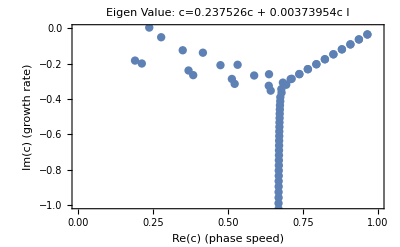

```mathematica
(*Plot eigenvalue spectrum (phase speed vs growth rate)*)ListPlot[data,PlotStyle->PointSize[0.015],Frame->True,FrameLabel->{"Re(c) (phase speed)","Im(c) (growth rate)"},PlotRange->{{0,1},{-1,0}},PlotLabel->"Eigen Value:\n c="<>ToString[NumberForm[Reveigvals[[1]],NumberFormat->(Row[{#1,"c",#3}]&)]]]
```

```mathematica
(*Orr-Sommerfeld spectrum of plane Poiseuille flow wave numbers alpha=0,beta=0 *)
```

```mathematica
alpha=0;
beta1=1;
```

```mathematica
F=-(1/(Rey))*(D4-2*beta1^2*D2+beta1^4*IdentityMatrix[nG+1]);
```

```mathematica
Mmat=ⅈ(D2-beta1^2IdentityMatrix[nG+1]);
```

```mathematica
(*4 BC~No Slip condtions,Gradient=0*)
```

```mathematica
Table[F[[1,j]]=0,{j,2,nG+1}];
F[[1,1]]=1;
Table[F[[nG+1,j]]=0,{j,1,nG}];
F[[nG+1,nG+1]]=1;
F[[2]]=D1[[1]];
F[[nG]]=D1[[nG+1]];
```

```mathematica
Table[Mmat[[1,j]]=0,{j,1,nG+1}];
Table[Mmat[[nG+1,j]]=0,{j,1,nG+1}];
Table[Mmat[[2,j]]=0,{j,1,nG+1}];
Table[Mmat[[nG,j]]=0,{j,1,nG+1}];
```

```mathematica
{eigvals1,eigvecs1}=Eigensystem[{F,Mmat}];
```

```mathematica
eigvalsSorted1=SortBy[eigvals1,Re];
```

```mathematica
data1=ReIm/@eigvalsSorted1;
```

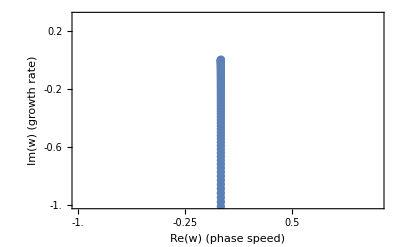

```mathematica
ListPlot[data1,PlotStyle->PointSize[0.015],Frame->True,FrameLabel->{"Re(w) (phase speed)","Im(w) (growth rate)"},PlotRange->{{-1.0,1.1},{-1,0.3}},GridLines->Automatic,FrameTicks->{Range[-1.0,2.0,0.15],Range[-1.0,0.2,0.2]}
]
```

```mathematica
vals=Transpose[{eigvals,eigvecs}];
```

```mathematica
valsSorted=SortBy[vals,{-Im[#[[1]]],Re[#[[1]]]}&];
```

```mathematica
modeA=SelectFirst[valsSorted,Abs[Re[#[[1]]]-.3121]<.008&][[2]];
```

```mathematica
(*Most unstable mode*)
modeP=SelectFirst[valsSorted,Abs[Re[#[[1]]]-1]<0.05&][[2]];
```

```mathematica
modeS=SelectFirst[valsSorted,Abs[Re[#[[1]]]-2/3]<0.01&][[2]];
```

```mathematica
vA=Join[Flatten[modeA]];
```

```mathematica
vP=Join[Flatten[modeP]];
```

```mathematica
vS=Join[Flatten[modeS]];
```

```mathematica
ygrid=Join[y];
```

```mathematica
Length[ygrid];
```

```mathematica
Length[vA];
```

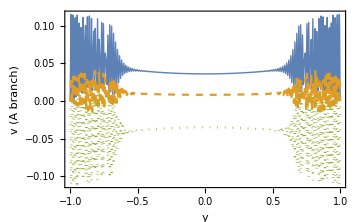

```mathematica
Show[ListLinePlot[{Transpose[{ygrid,Abs[vA]}],Transpose[{ygrid,Re[vA]}],Transpose[{ygrid,Im[vA]}]},PlotStyle->{Thick,Dashed,Dotted},PlotRange->All,Frame->True,FrameLabel->{"y","v (A branch)"}],ImageSize->Medium]
```

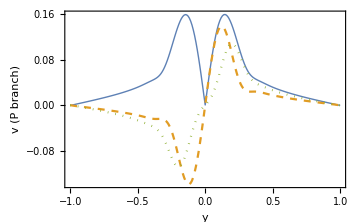

```mathematica
Show[ListLinePlot[{Transpose[{ygrid,Abs[vP]}],Transpose[{ygrid,Re[vP]}],Transpose[{ygrid,Im[vP]}]},PlotStyle->{Thick,Dashed,Dotted},PlotRange->All,Frame->True,FrameLabel->{"y","v (P branch)"}],ImageSize->Medium]
```

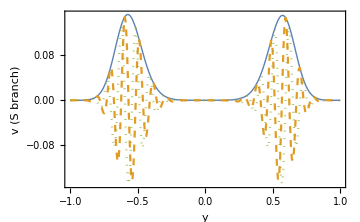

```mathematica
Show[ListLinePlot[{Transpose[{ygrid,Abs[vS]}],Transpose[{ygrid,Re[vS]}],Transpose[{ygrid,Im[vS]}]},PlotStyle->{Thick,Dashed,Dotted},PlotRange->All,Frame->True,FrameLabel->{"y","v (S branch)"}],ImageSize->Medium]
```